```mathematica
Clear["Global`*"];
L=1; M=10; Δt = 0.05; Δx = L/M; ζ=1/4;
```

```mathematica
T0[x_] = Sin[π x / L ] // N;
T[0,n_]:=0;
T[M,n_] := 0;
S[j_,n_] = 0;
```

```mathematica
sol[0] = Table[T[j,0]-> T0[j Δx], {j,1,M-1}]
```

{T[1,0]→0.309017,T[2,0]→0.587785,T[3,0]→0.809017,T[4,0]→0.951057,T[5,0]→1.,T[6,0]→0.951057,T[7,0]→0.809017,T[8,0]→0.587785,T[9,0]→0.309017}

```mathematica
sol[n_]:=sol[n] = 
Module[{vars,eqns},
(*define the variables*)
vars = Table[T[j,n],{j,1,M-1}];
(* define equations substituting for the values of T determined at last timestep*)
eqns = Table[T[j,n]-T[j,n-1] == 1/2 (Δt (S[j,n]+S[j,n-1])+ (ζ Δt)/Δx^2(T[j+1,n]-2 T[j,n]+
T[j-1,n]+T[j+1,n-1]-2 T[j,n-1] +
T[j-1,n-1])),{j,1,M-1}]/.sol[n-1];
(*solve the equations*)
Solve[eqns,vars][[1]]]
```

```mathematica
CrankNicholson=Table[ListPlot[Table[{Δx j, T[j,n]},{j,0,M}]/.sol[n],
Joined->True, PlotRange->{{0,L},{0,1}},
AxesLabel->{"x",""},PlotLabel->"T[x,t],t=" <> ToString[Δt n],
DisplayFunction->Identity],{n,0,40,5}];
exact=Table[Plot[ⅇ^(-π^2 ζ t / L^2)Sin[Pi x/L],{x,0,L}, DisplayFunction->Identity,
PlotStyle->RGBColor[1,0,0]],{t,0,40 Δt, 5 Δt}];
Table[Show[CrankNicholson[[n]],exact[[n]],DisplayFunction->$DisplayFunction],{n,1,Length[exact]}];
```

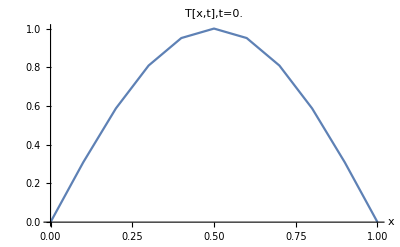
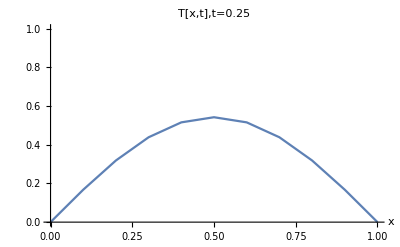
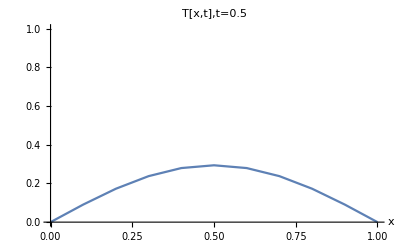
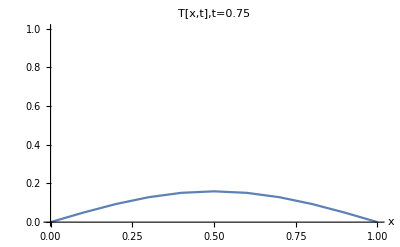
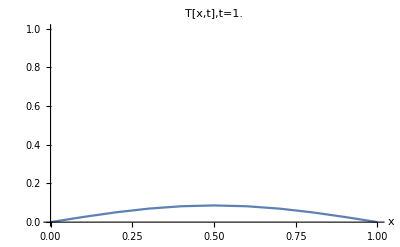
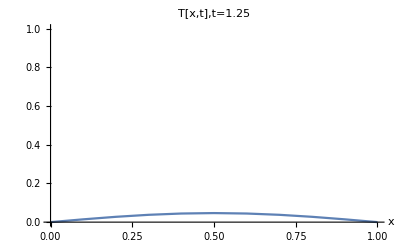
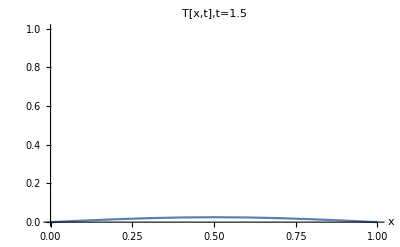
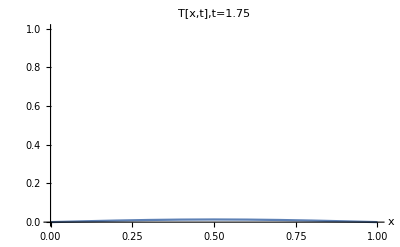

```mathematica
%46
```

```mathematica
Tsol = Interpolation[Flatten[Table[Table[{j Δx, n Δt, T[j,n]},{j,0,M}]/.sol[n],{n,0,25}],1]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[Tsol[x,t],{x,0,1},{t,0,1.25},
AxesLabel->{"x","t","T[x,t]"}]
```

-Graphics3D-